```mathematica
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(*MOT geometry*)
MOTIR= 68.326 / 2; (*mm*)
Epoxy=0;(*mm epoxy thickness*)
NumTurns = 3;(*turns per layer*)
MOTI =50;(*A*)(****************play with this***************************)
CoilOut = 4.2;(*outer diameter of wire - mm*)
CoilIn = 1.8;(*inner diameter of wire (cooling part?) - mm*)
MOTOR = MOTIR+NumTurns*CoilOut ;(*mm*)
MOTJ = MOTI/((CoilOut)^2); (*A/mm2*)
NumLayers =6;
height =NumLayers*CoilOut; (*mm*)
sep = 53;(*mm near-Holmholtz*); (****************play with this***************************)
Distance=sep+height;
Radius = (MOTIR+MOTOR)/2;
lx=0;(*mm lengths of straight parts long x-axis of the racetrack*)
ly=0;(*mm lengths of straight parts long y-axis of the racetrack*)
(* angle of coils viewed projected onto the z-x plane. Amount of rotation about the y-axis*)
(*theta = 0* 180/π;*)
(*Create coils using radia*)
(*Keep the difference of Helmholtz and anti-Helmholtz in mind when you create coils!*)
topcoil=radObjRaceTrk[{0,0,Distance/2},{MOTIR,MOTOR},{lx,ly},height,100,MOTJ];
radTrfOrnt[topcoil,radTrfRot[{0,0,0},{0,1,0},π/2]];
bottomcoil=radObjRaceTrk[{0,0,Distance/2},{MOTIR,MOTOR},{lx,ly},height,100,MOTJ];
radTrfOrnt[bottomcoil,radTrfRot[{0,0,0},{0,1,0},-π/2]];
MOT=radObjCnt[{topcoil,bottomcoil}];
(*Draw graphical representation*)
MOTDR=radObjDrw[MOT];
Show[Graphics3D[MOTDR],Axes->True]

(*I think that the y-axis is through the center of the coils?*)
(* plot results *)
rmax = 200;
numpts = 500;
(* center of coordinates *)
xcenter =0;
ycenter =1;
zcenter =0;
BZoffset = 0; (*G*)

MOTIR+NumTurns*CoilOut/2-height/2(*mm exact Holmholtz*)
sep
Distance
NumTurns*CoilOut
NumLayers*CoilOut
```

-Graphics3D-

27.863

53

78.2

12.6

25.2

```mathematica
MOTOR
height
```

46.763

25.2

Plotting the B field as a function of distance.

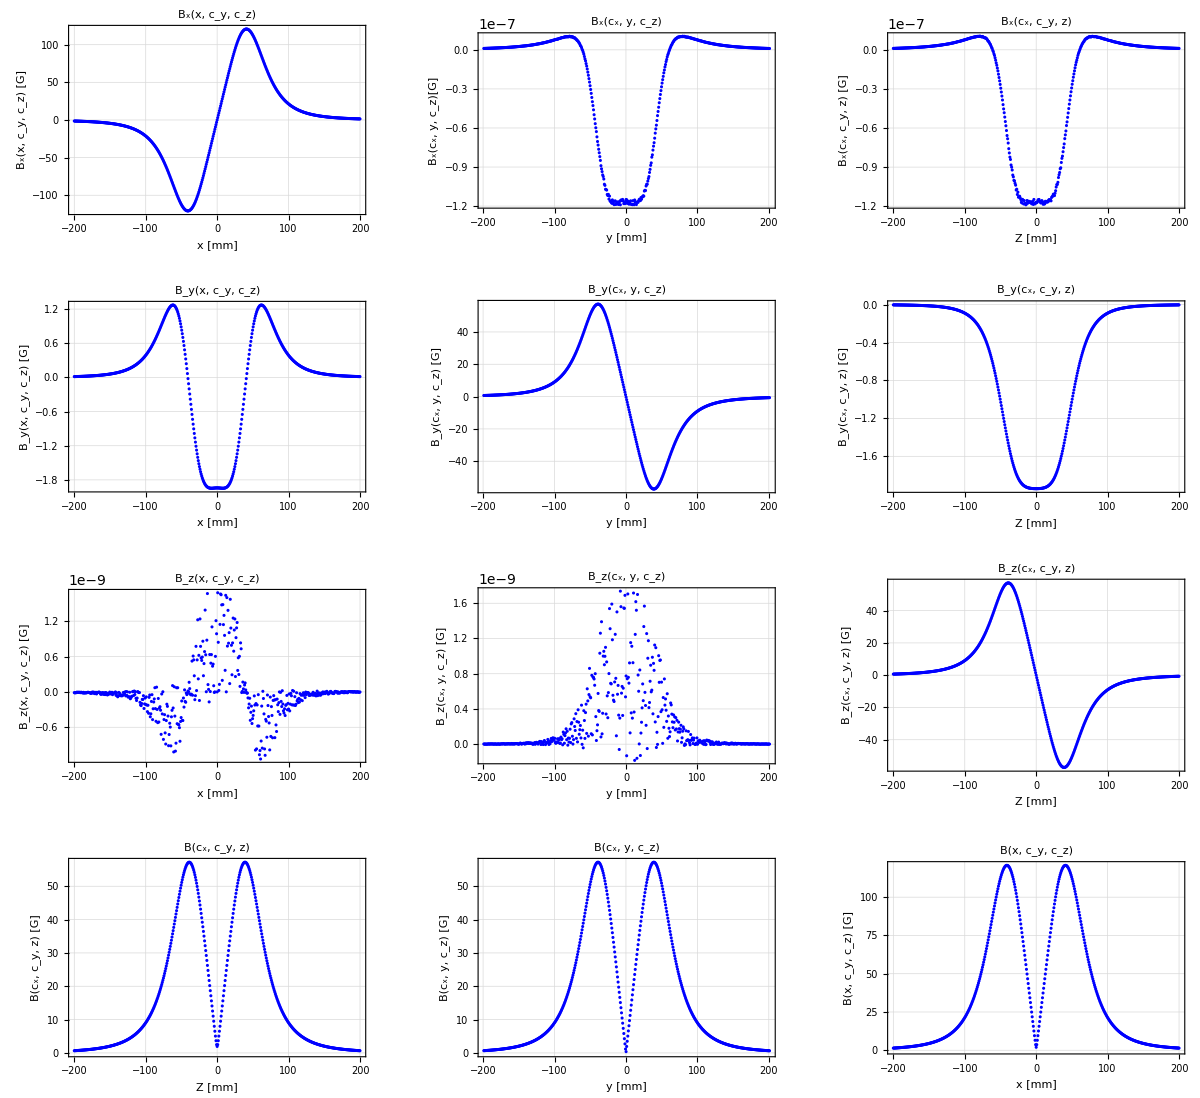

```mathematica
(*Bz*)
BzZaxis=Table[{z,BZoffset + 10^4*radFld[MOT,"Bz",{xcenter, ycenter,z}]},{z,zcenter-rmax,zcenter + rmax, 2*rmax/numpts}];
BzYaxis = Table[{y,BZoffset +10^4*radFld[MOT,"Bz",{xcenter,y, zcenter}]},{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
BzXaxis = Table[{x, BZoffset +10^4 * radFld[MOT, "Bz", {x, ycenter, zcenter}]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
BzZplot=ListPlot[BzZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B_z(c_x, c_y, z) [G]"},PlotLabel->"B_z(c_x, c_y, z)",PlotStyle->{Blue}];
BzYplot = ListPlot[BzYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B_z(c_x, y, c_z) [G]"},PlotLabel->"B_z(c_x, y, c_z)",PlotStyle->{Blue}];
BzXplot = ListPlot[BzXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B_z(x, c_y, c_z) [G]"},PlotLabel->"B_z(x, c_y, c_z)",PlotStyle->{Blue}];
(*GraphicsRow[{BzXplot, BzYplot, BzZplot}, PlotLabel->"B_z Field"]*)
(*Bx*)
BxZaxis=Table[{z,10^4*radFld[MOT,"Bx",{xcenter,ycenter,z}]},{z,zcenter-rmax,zcenter +rmax, 2*rmax/numpts}];
BxYaxis = Table[{y,10^4*radFld[MOT,"Bx",{xcenter,y,zcenter}]},{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
BxXaxis = Table[{x, 10^4 * radFld[MOT, "Bx", {x, ycenter, zcenter}]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
BxZplot=ListPlot[BxZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B_x(c_x, c_y, z) [G]"},PlotLabel->"B_x(c_x, c_y, z)",PlotStyle->{Blue}];
BxYplot = ListPlot[BxYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B_x(c_x, y, c_z)[G]"},PlotLabel->"B_x(c_x, y, c_z)",PlotStyle->{Blue}];
BxXplot = ListPlot[BxXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B_x(x, c_y, c_z) [G]"},PlotLabel->"B_x(x, c_y, c_z)",PlotStyle->{Blue}];
(*GraphicsRow[{BxXplot, BxYplot, BxZplot}, PlotLabel->"B_xField"]*)
(*By*)
ByZaxis=Table[{z,10^4*radFld[MOT,"By",{xcenter,ycenter,z}]},{z,zcenter-rmax,zcenter+rmax, 2*rmax/numpts}];
ByYaxis = Table[{y,10^4*radFld[MOT,"By",{xcenter,y,zcenter}]},{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
ByXaxis = Table[{x, 10^4 * radFld[MOT, "By", {x, ycenter, zcenter}]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
ByZplot=ListPlot[ByZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B_y(c_x, c_y, z) [G]"}, PlotLabel->"B_y(c_x, c_y, z)", PlotStyle->{Blue}];
ByYplot = ListPlot[ByYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B_y(c_x, y, c_z) [G]"},PlotLabel->"B_y(c_x, y, c_z)", PlotStyle->{Blue}];
ByXplot = ListPlot[ByXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B_y(x, c_y, c_z) [G]"},PlotLabel->"B_y(x, c_y, c_z)", PlotStyle->{Blue}];
(*|B|*)
BZaxis = Table[{z, Sqrt[Total[( {0, 0, BZoffset}  + 10^4 * radFld[MOT, "B", {xcenter, ycenter, z}] )^2]]}, {z,zcenter-rmax,zcenter+rmax, 2*rmax/numpts}];
BYaxis = Table[{y,Sqrt[Total[( {0, 0, BZoffset}  + 10^4 * radFld[MOT, "B", {xcenter,y, zcenter}] )^2]]}, {y, ycenter-rmax, ycenter+rmax, 2*rmax/numpts}];
BXaxis = Table[{x,Sqrt[Total[( {0, 0, BZoffset}  + 10^4 * radFld[MOT, "B", {x,ycenter, zcenter}] )^2]]}, {x, xcenter-rmax, xcenter+rmax, 2*rmax/numpts}];
BZplot=ListPlot[BZaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [mm]","B(c_x, c_y, z) [G]"}, PlotLabel->"B(c_x, c_y, z)", PlotStyle->{Blue}];
BYplot = ListPlot[BYaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [mm]","B(c_x, y, c_z) [G]"},PlotLabel->"B(c_x, y, c_z)", PlotStyle->{Blue}];
BXplot = ListPlot[BXaxis,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [mm]","B(x, c_y, c_z) [G]"},PlotLabel->"B(x, c_y, c_z)", PlotStyle->{Blue}];

(*GraphicsRow[{ByXplot, ByYplot, ByZplot}, PlotLabel->"B_y Field"]*)
GraphicsGrid[{{BxXplot, BxYplot, BxZplot}, {ByXplot, ByYplot, ByZplot}, {BzXplot, BzYplot, BzZplot}, {BZplot, BYplot, BXplot}}, PlotLabel->"MOT Fields", Frame->True, ImageSize->Full]

dist =  N[Table[z,{z,zcenter-rmax,zcenter +rmax, 2*rmax/numpts}]];
Bxx = Table[10^4*radFld[MOT,"Bx",{x,ycenter,zcenter}],{x,xcenter-rmax,xcenter+rmax,2*rmax/numpts}];
Byy = Table[10^4*radFld[MOT,"By",{xcenter,y,zcenter}],{y,ycenter-rmax,ycenter+rmax,2*rmax/numpts}];
Bzz = Table[10^4*radFld[MOT,"Bz",{xcenter,ycenter,z}],{z,zcenter-rmax,zcenter+rmax,2*rmax/numpts}];
(*Export["//128.112.86.75//lithium//Simulation//Magnet Coils//MOT Coils//Mot_fields.tsv",Transpose[{dist, Bxx,Byy,Bzz}]];*)
```

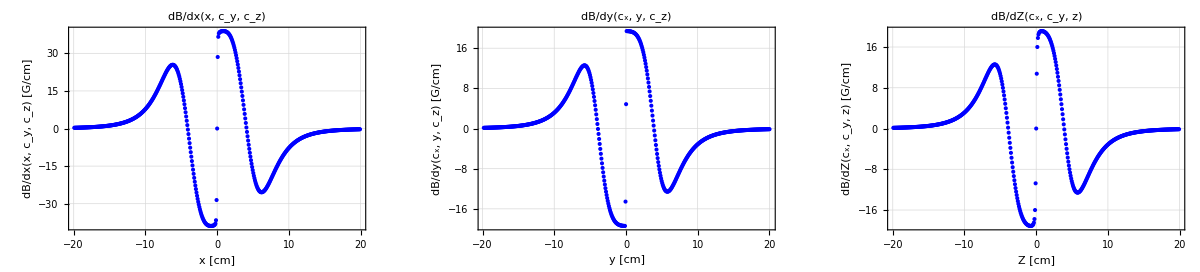

```mathematica
(* G / cm*)
(* |B|derivatives along x,y,z in cm (convert mm->cm)*)(*helper:central-difference derivative from List[{pos,val}] data*)d1[data_]:=Module[{x=data[[All,1]],f=data[[All,2]],dx},dx=x[[2]]-x[[1]];
Table[{x[[i]],(f[[i+1]]-f[[i-1]])/(2 dx)},{i,2,Length[x]-1}]];

(*build derivative datasets from your existing|B|axis tables (G/mm)*)
dBZaxisMM=d1[BZaxis];
dBYaxisMM=d1[BYaxis];
dBXaxisMM=d1[BXaxis];

(*convert:position:mm->cm (÷10) gradient:G/mm->G/cm (×10)*)
dBZaxisCM=Table[{dBZaxisMM[[i,1]]/10,10*dBZaxisMM[[i,2]]},{i,Length[dBZaxisMM]}];

dBYaxisCM=Table[{dBYaxisMM[[i,1]]/10,10*dBYaxisMM[[i,2]]},{i,Length[dBYaxisMM]}];

dBXaxisCM=Table[{dBXaxisMM[[i,1]]/10,10*dBXaxisMM[[i,2]]},{i,Length[dBXaxisMM]}];

(*plots in cm*)
dBZplotCM=ListPlot[dBZaxisCM,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Z [cm]","dB/dZ(\!\(\*SubscriptBox[\(c\), \(x\)]\), \!\(\*SubscriptBox[\(c\), \(y\)]\), z) [G/cm]"},PlotLabel->"dB/dZ(\!\(\*SubscriptBox[\(c\), \(x\)]\), \!\(\*SubscriptBox[\(c\), \(y\)]\), z)",PlotStyle->{Blue}];

dBYplotCM=ListPlot[dBYaxisCM,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"y [cm]","dB/dy(\!\(\*SubscriptBox[\(c\), \(x\)]\), y, \!\(\*SubscriptBox[\(c\), \(z\)]\)) [G/cm]"},PlotLabel->"dB/dy(\!\(\*SubscriptBox[\(c\), \(x\)]\), y, \!\(\*SubscriptBox[\(c\), \(z\)]\))",PlotStyle->{Blue}];

dBXplotCM=ListPlot[dBXaxisCM,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"x [cm]","dB/dx(x, \!\(\*SubscriptBox[\(c\), \(y\)]\), \!\(\*SubscriptBox[\(c\), \(z\)]\)) [G/cm]"},PlotLabel->"dB/dx(x, \!\(\*SubscriptBox[\(c\), \(y\)]\), \!\(\*SubscriptBox[\(c\), \(z\)]\))",PlotStyle->{Blue}];

GraphicsRow[{dBXplotCM,dBYplotCM,dBZplotCM},PlotLabel->"Derivatives of |B| (G/cm)",ImageSize->Full]
```

```mathematica
(* water cooling estimates*)
LperLayer = 0;
For[n=0,n<NumTurns,n++,LperLayer=LperLayer+2*Pi*(MOTIR+CoilOut*n)];
Ltotal=0.001*(LperLayer*NumLayers)+1; (*m - additional length leads - unsure for now*)(*L for entire MOT coil: 2 coils each with 6 layers and each layer with 3 turns + 2 leads of 0.5m each*)
RhoCopper = 1.68*10^(−8);(*in Ohm-m*)
CrossSection = ((CoilOut-Epoxy)^2-CoilIn^2)*10^(-6);
(*Rho=RhoCopper/CrossSection;*)
pipeDiaIn=CoilIn*39.3701*0.001;(*pipe inner diameter in inch*)
```

```mathematica
pdissipated=RhoCopper*MOTI^2*Ltotal / CrossSection(*in W*)
```

15.5714

```mathematica
PressureDrop=80(*psi*);
flowRateGal =((PressureDrop*140^1.85*(pipeDiaIn)^4.87)/(4.52*(Ltotal*3.28084)))^0.54(*in Gal/min*)
```

0.132834

```mathematica
flowRate=flowRateGal/0.000264172;(*convert GPM to mL/min*)
deltaT=14.3*pdissipated/flowRate (*in deg C*)
```

0.442832